0.00444653

0.0260687

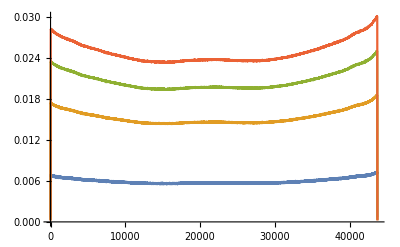

9.16211

1.0157

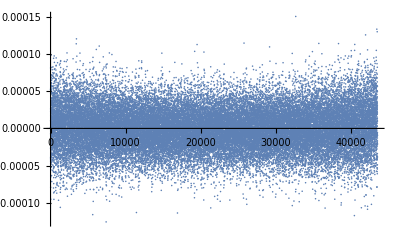

```mathematica
dBmToWatts[x_]:=10^(x/10)*10^9;
GaussMatrix[α_]:=GaussianMatrix[α][[2,All]]//Normalize;
Test[l_]:=Insert[ConstantArray[0,2*l],1,l/2]
data=Import["/home/bephillips2/workspace/Electric_Tiger_Control_Code/data/45_12_12_11.08.2016/SA_F0.csv","CSV"];
choppeddata = Take[data,{12,Length[data]}]//Flatten;
wattsdata=Map[dBmToWatts,choppeddata];
min = Min[wattsdata]
min2 = Min[ListConvolve[GaussMatrix[20],wattsdata]]
Table[ListConvolve[GaussMatrix[i],wattsdata,{1,-1},0],{i,1,20,5}]//ListLinePlot
size = Length[ListConvolve[GaussMatrix[50],wattsdata] ];
size2 = Length[wattsdata];
convolved = ListConvolve[GaussMatrix[50],wattsdata];
cnorm = Norm[convolved]
resized = ArrayResample[wattsdata,size];
rnorm = Norm[resized]
ListPlot[ resized -(rnorm/cnorm)*convolved ]
```